```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/15-on-15n_0423-0749.csv", Numeric->True];
data=Delete[data, 1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
```

```mathematica
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
{baselineWall,gnnWall}=SortBy[{baselineWall,gnnWall}ᵀ,First]ᵀ;
```

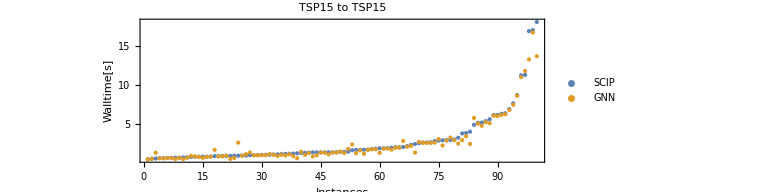

```mathematica
plot=Show[
ListPlot[{baselineWall,gnnWall},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,Automatic},
PlotLabel->Style["TSP15 to TSP15"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-15.png",plot];
```

```mathematica
Mean[baselineWall-gnnWall]/Mean[baselineWall]*100
```

5.69968